```mathematica
Quit[]
```

## Set Notebook Directory.

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Krzysztof\Desktop\Magisterka\Praca-magisterska\Code\Maxim-muon-scattering

## Initialise all necessary lists.

```mathematica
qValuesList = {} (*comoving momentum list*);
maValuesList={} (*Initialize list: mass of axion, [eV]*);
AparameterList = {} (*Initialize list: one of the parameter, which we need to fit*);
bparameterList = {} (*Initialize list: one of the parameter, which we need to fit*);
μparameterList = {} (*Initialize list: one of the parameter which, we need to fit*);
```

## Read data from file.

The range of comoving momentum of our interest is in range [0, 20] (200 points distributed logarithmically from 1e-4 to 20.0). File contains the value of the: `f(q) * q^2`, where `f(q)` is function distribution of axion particles. We have those function distribution for specific values of the axion masses: `m_a`.

```mathematica
(********** Step 1:Set q values**********)
```

```mathematica
(*Define a function for logarithmic spacing*)
LogSpace[start_,end_,n_]:=Exp[Subdivide[Log[start],Log[end],n-1]]
(*Use the function to generate 200 points from 1e-4 to 20.0*)
qValuesList=LogSpace[1*10^-4,20.0,200];
(********** Step 2:Import the CSV file, `Distributions.csv` **********)
data=Import["ma_distributions_mu_scattering.dat","CSV"];
(*** ma list [eV]]***)
maValuesList=10^9*data[[2;;,1]]; (*Skip the header row and extract the first element from each subsequent row: there will be ma value*)

(*** distribution list ***)
(*Separate header and data*)
header=data[[1]];                 (*Extract the header row*)
dataWithoutHeader=data[[2;;]];   (*Extract the data without the header row*)

(*Skip the first element in each data row*)
distributionsQPow2=Rest/@dataWithoutHeader; (*Output the processed data without header, `f(q) * q^2*)
(*Here we have to divide each elelemt by q^2, `f(q)`*)
distributions = Map[MapThread[Times,{#,qValuesList^-2}]&,distributionsQPow2];
(* f(q) * q^3*)
distributionsQPow3 = Map[MapThread[Times,{#,qValuesList}]&,distributionsQPow2];

(********** Step 4: set some constants **********)
NumberOfDistributions = Length[maValuesList];

(********** Step 5: Check List, sanity checks **********)
(*Print["qValuesList", qValuesList, "len(qValuesList)=", Length[qValuesList]];
Print["faValuesList", faValuesList, "len(faValuesList)=", Length[faValuesList]];
Print["maValuesList", maValuesList, "len(maValuesList)=", Length[maValuesList]];*)
(*Print["distributionsQPow3",distributionsQPow3]*)
Print["len(distributionsQPow3)",Length[distributionsQPow3]]
Print["maValuesList", maValuesList, "len(maValuesList)=", Length[maValuesList]]
```

len(distributionsQPow3)200

maValuesList{6.2302,6.08768,5.94842,5.81234,5.67938,5.54946,5.42251,5.29847,5.17726,5.05883,4.9431,4.83002,4.71953,4.61157,4.50608,4.403,4.30227,4.20385,4.10769,4.01372,3.9219,3.83219,3.74452,3.65886,3.57516,3.49338,3.41347,3.33538,3.25908,3.18453,3.11168,3.04049,2.97094,2.90298,2.83657,2.77168,2.70828,2.64632,2.58579,2.52663,2.46883,2.41236,2.35717,2.30325,2.25056,2.19908,2.14877,2.09962,2.05159,2.00466,1.9588,1.91399,1.8702,1.82742,1.78562,1.74477,1.70486,1.66586,1.62775,1.59051,1.55413,1.51858,1.48384,1.44989,1.41673,1.38432,1.35265,1.32171,1.29147,1.26193,1.23306,1.20485,1.17729,1.15036,1.12404,1.09833,1.07321,1.04866,1.02467,1.00123,0.978322,0.955942,0.934074,0.912706,0.891828,0.871426,0.851492,0.832013,0.81298,0.794382,0.77621,0.758454,0.741104,0.72415,0.707585,0.691398,0.675582,0.660127,0.645026,0.630271,0.615853,0.601765,0.587999,0.574548,0.561404,0.548562,0.536013,0.523751,0.51177,0.500063,0.488624,0.477446,0.466524,0.455852,0.445424,0.435234,0.425278,0.415549,0.406043,0.396755,0.387679,0.37881,0.370145,0.361677,0.353403,0.345319,0.33742,0.329701,0.322159,0.314789,0.307588,0.300552,0.293676,0.286958,0.280394,0.27398,0.267712,0.261588,0.255604,0.249757,0.244043,0.238461,0.233006,0.227675,0.222467,0.217378,0.212405,0.207546,0.202799,0.198159,0.193626,0.189197,0.184869,0.18064,0.176508,0.17247,0.168524,0.164669,0.160902,0.157222,0.153625,0.150111,0.146677,0.143321,0.140043,0.136839,0.133709,0.13065,0.127661,0.124741,0.121888,0.119099,0.116375,0.113713,0.111111,0.10857,0.106086,0.103659,0.101288,0.0989708,0.0967067,0.0944945,0.0923329,0.0902207,0.0881568,0.0861401,0.0841696,0.0822441,0.0803627,0.0785244,0.0767281,0.0749728,0.0732578,0.0715819,0.0699444,0.0683444,0.066781,0.0652533,0.0637606,0.062302}len(maValuesList)=200

## Collect data into groups and set approx distribution function.

Here we try to transpose data in such a way to have a value of the comoving momenta and proper value of the function distribution (maybe multiply with some power of comoving momenta) - the less operation with data, the better results I will get. Important in the third line you set how look the `axion distribution function` in shortcut: `AxDistFunction`. In generall I suggest to use: `f(q)*q^3`.

```mathematica
(*Helpfull function to create Transposed data, remeber that `i` will refer to vale of `f_a` in `faList`.*)
transposeData[i_,list_,listOfLists_List]:=Transpose[{list,listOfLists[[i]]}]
(*Transpose data numerous of times*)
AxDistFunctionTabList=Table[transposeData[i,qValuesList,distributionsQPow3],{i,NumberOfDistributions}]; (* f(q)*q^3 *)
AxDistFunctionList=Table[Interpolation[AxDistFunctionTabList[[i]],Method->"Spline",InterpolationOrder->3],{i,NumberOfDistributions}];
(*Defined the approx axion distribution function, `f(q)*q^3`*)
(*fApprox[x_,A_,b_,μ_]:=x^3*A(1/(Exp[x/b + μ]-1))*)
(*fApprox[x_,A_,b_,μ_]:=x^2 √(1+x^2)*(Exp[A(√(1+x^2)-b)+μ])^-1*)
(*fApprox[x_,A_,b_,μ_]:=x^2(Exp[A(√(1+x^2)-b)+μ])^-1*)
(*fApprox[x_,A_,b_]:=x^2(Exp[A(√(1+x^2)-b)])^-1*)
(*fApprox[x_,A_,b_]:=x^2(Exp[A √(1+x^2)-b])^-1*)
fApprox[x_,A_,b_,μ_]:=x^2(Exp[A √(1+x^2)-b]+μ)^-1
```

## (Optional) sanity check of interpolation .

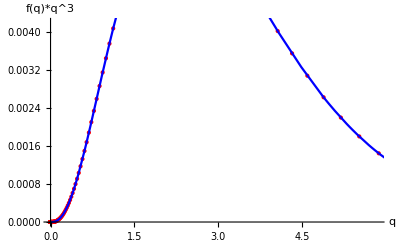

```mathematica
(*Plot original data points and the interpolated function on the same plot*)Show[ListPlot[AxDistFunctionTabList[[199]],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"q","f(q)*q^3"}],Plot[AxDistFunctionList[[199]][x],{x,Min[qValuesList],Max[qValuesList]},PlotStyle->Blue]]
```

## (Optional) select a distribution and make a fit - update way of finding fit.

best fit parameters: {A→0.842368,b→0.70378,μ→0.380099}[]

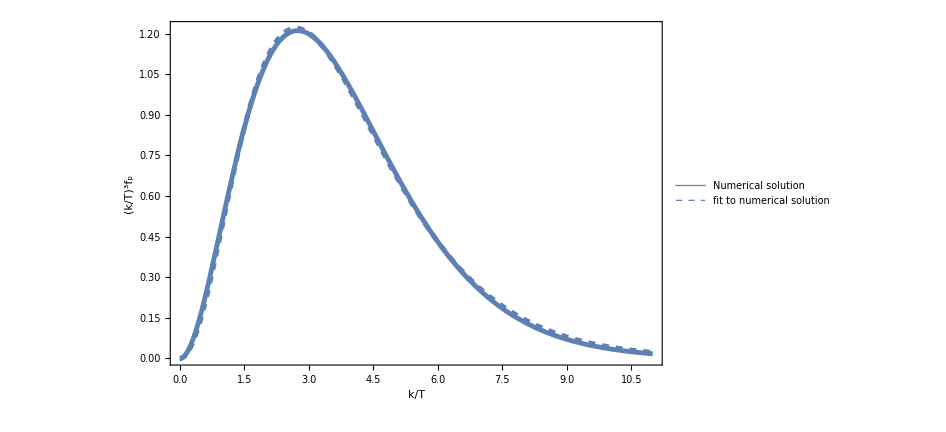

```mathematica
(********** Step 1: Settings to make a fit **********)
SelectedDist = AxDistFunctionList[[1]];
xmin = 0.0;
xmax = 11;
step = 0.005;
dataToFit=Table[{x,SelectedDist[x]},{x,xmin,xmax,step}];
(********** Step 2: Perform the nonlinear fit **********)
fit=NonlinearModelFit[dataToFit,{fApprox[x,A,b,μ]},{A,b,μ},x,
Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->100}}];
(*fit=NonlinearModelFit[dataToFit,{fApprox[x,A,b]},{A,b},x,
Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->100}}];*)
(********** Step 3: Optional information **********)
(*Extract best-fit parameters*)
bestFitParams=fit["BestFitParameters"];
Print["best fit parameters:"bestFitParams[]];
(*Visualize the fit*)
(*Show[ListPlot[data],Plot[fit[x],{x,xmin,xmax},PlotStyle->Red]]*)

(********** Step 4: Plot distribution and fit **********)
Plot[{SelectedDist[x], fit[x]},{x,0,11},Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},{Dashed,Thickness[0.005],ColorData[97,1]},{Thickness[0.005],Orange,ColorData[97,2]}},

PlotLegends->{"Numerical solution","fit to numerical solution"},
ImageSize-> 700]
```

## Find all parameters for each distribution function .

We already create two list: `maValuesList`. Now we have to read the distribution function and find parameters, which describes best fit to data stored in `AxDistFunctionTabList`. We need this because in the end we are looking for function: A(m_a), b(m_a) and μ(m_a), where A, b and μ are parameters which we will find out.

```mathematica
(*clear up*)
AparameterList = {};
bparameterList = {};
μparameterList = {};
(*find parameters*)
For[i=1,i<=NumberOfDistributions,i++,
If[Mod[i,10]==0,Print["step: ",i]];
(********** Step 1: Settings to make a fit **********)
SelectedDist = AxDistFunctionList[[i]];
xmin = 0.0;
xmax = 11;
step = 0.005;
dataToFit=Table[{x,SelectedDist[x]},{x,xmin,xmax,step}];
(********** Step 2: Perform the nonlinear fit **********)
fit=NonlinearModelFit[dataToFit,{fApprox[x,A,b,μ]},{A,b,μ},x,
Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->100}}];
(*fit=NonlinearModelFit[dataToFit,{fApprox[x,A,b]},{A,b},x,
Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->100}}];*)

(********** Step 3: Find the best parameters and Append them to right List **********)
bestFitParams={A,b,μ}/.fit["BestFitParameters"];
(*bestFitParams={A,b}/.fit["BestFitParameters"];*)
AppendTo[AparameterList,bestFitParams[[1]] ];
AppendTo[bparameterList,bestFitParams[[2]] ];
AppendTo[μparameterList,bestFitParams[[3]] ];
]
(***Test my results***)
(*Print["AparameterList", AparameterList, "len(AparameterList)", Length[AparameterList]];
Print["bparameterList", bparameterList, "len(bparameterList)", Length[bparameterList]];*)
(*Print["μparameterList", μparameterList, "len(μparameterList)", Length[μparameterList]];*)
```

step: 10

step: 20

step: 30

step: 40

step: 50

step: 60

step: 70

step: 80

step: 90

step: 100

step: 110

step: 120

step: 130

step: 140

step: 150

step: 160

step: 170

step: 180

step: 190

step: 200

## (Optional) Find function A(m_a), b(m_a) and μ(m_a).

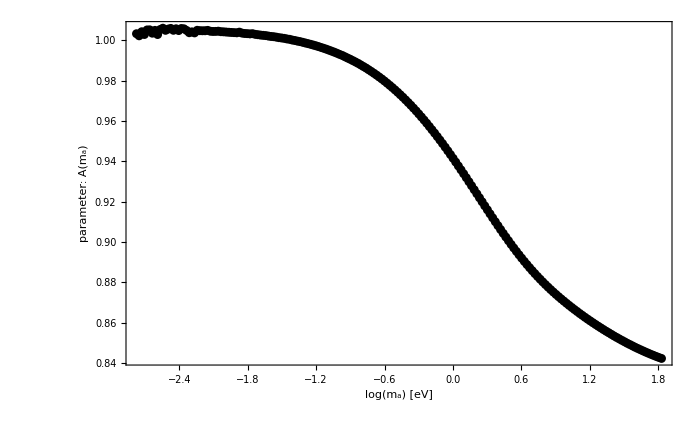

```mathematica
(********************************************* deal with parameter A ****************************************************)
dataParameterA = Transpose[{Log[maValuesList],AparameterList}]; (*Combine maValuesList and AparameterList into a list of data points*)
(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[AparameterList];
xmax = Max[Log[maValuesList]];
ymax = Max[AparameterList];

(********Plot the data with black dots********)
Show[ListPlot[dataParameterA,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: A(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700]
]
```

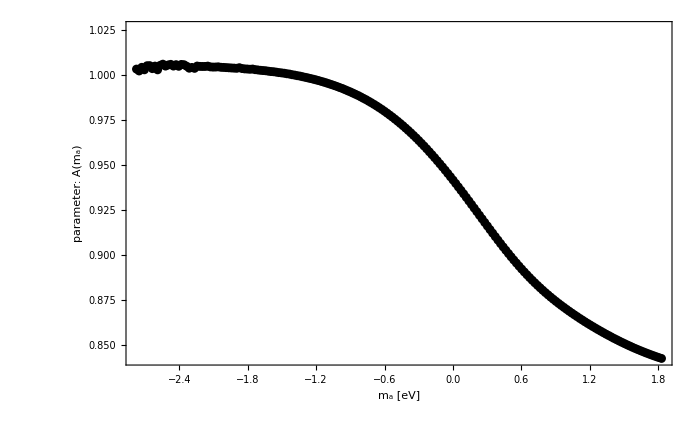

```mathematica
(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[AparameterList];
xmax =Max[Log[maValuesList]];
ymax = Max[AparameterList]+0.02;

(******** Plot the data with black dots ********)
Show[ListPlot[dataParameterA,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: A(m_a)",None},{"m_a [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700]
]
```

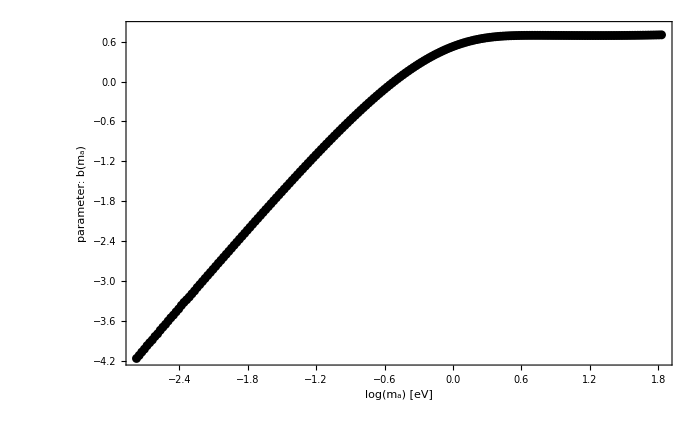

```mathematica
(********************************************* deal with parameter b ****************************************************)
dataParameterb = Transpose[{Log[maValuesList],bparameterList}]; (*Combine maValuesList and AparameterList into a list of data points*)
(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[bparameterList];
xmax =Max[Log[maValuesList]];
ymax = Max[bparameterList]+0.1;
(******** Plot the data with black dots ********)
Show[ListPlot[dataParameterb,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: b(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700]
]
```

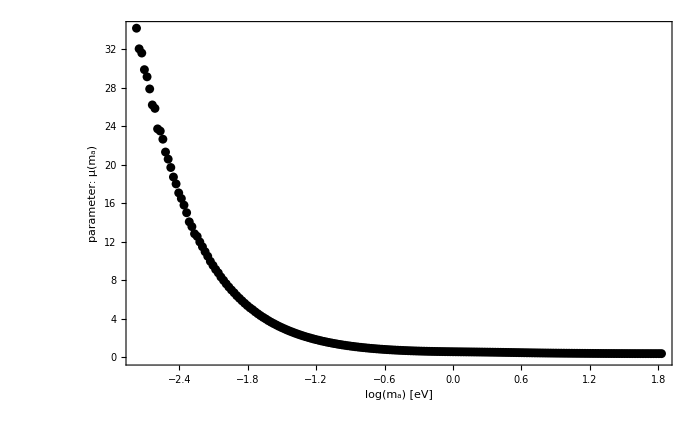

```mathematica
(********************************************* deal with parameter μ ****************************************************)
dataParameterμ = Transpose[{Log[maValuesList],μparameterList}]; (*Combine maValuesList and AparameterList into a list of data points*)
(********to proper work with plot********)
xmin = Min[Log[maValuesList]];
ymin = Min[μparameterList]-0.5;
xmax =Max[Log[maValuesList]];
ymax = Max[μparameterList];

(******** Plot the data with black dots ********)
Show[ListPlot[dataParameterμ,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: μ(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700]
]
```

## Find fit funtion : A (m_a), b (m_a) and μ (m_a)

FittedModel[0.941519-0.0813223 x-0.0199458 x^2+0.0259998 x^3+0.0158489 x^4-«21» x^5-«21» «1»+«23» x^7+0.00186323 x^8+0.000433136 x^9-0.000135033 x^10-0.0000665765 x^11-7.4609×10^-6 x^12]

0.941519-0.0813223 x-0.0199458 x^2+0.0259998 x^3+0.0158489 x^4-0.00690196 x^5-0.00789832 x^6+0.0000315946 x^7+0.00186323 x^8+0.000433136 x^9-0.000135033 x^10-0.0000665765 x^11-7.4609×10^-6 x^12

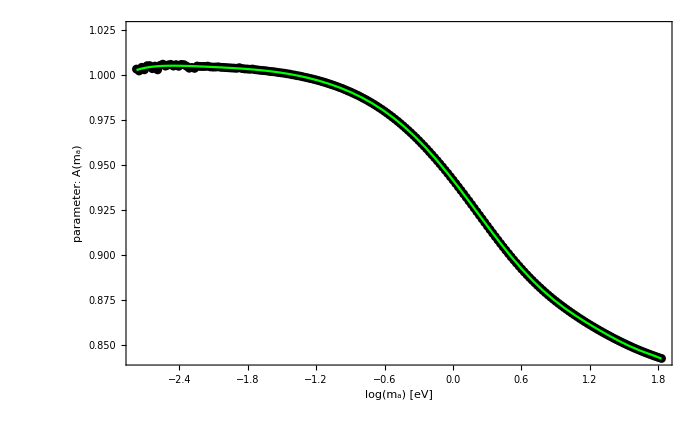

```mathematica
(********************************************* deal with parameter A ****************************************************)
(*Combine maValuesList and AparameterList into a list of points*)
dataParameterA = Transpose[{Log[maValuesList],AparameterList}]; 
(*Use FindFormula to find a suitable model for the data*)
polyModA=LinearModelFit[dataParameterA,Table[x^i,{i,1,12}],x]
polyModA["BestFit"]

(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[AparameterList];
xmax = Max[Log[maValuesList]];
ymax = Max[AparameterList]+0.02;
input=Log[maValuesList];
(******** plotting ********)
Show[ListPlot[dataParameterA,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: A(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700],
Plot[polyModA[x],{x,Min@input,Max@input},PlotStyle->Green]
]
```

FittedModel[0.526364+0.648989 x-0.726367 x^2+0.0726076 x^3+0.229016 x^4+0.0075853 x^5-«20» «1»-0.010611 x^7+0.0103606 x^8+0.0024378 x^9-0.000575171 x^10-0.000159403 x^11]

0.526364+0.648989 x-0.726367 x^2+0.0726076 x^3+0.229016 x^4+0.0075853 x^5-0.0669409 x^6-0.010611 x^7+0.0103606 x^8+0.0024378 x^9-0.000575171 x^10-0.000159403 x^11

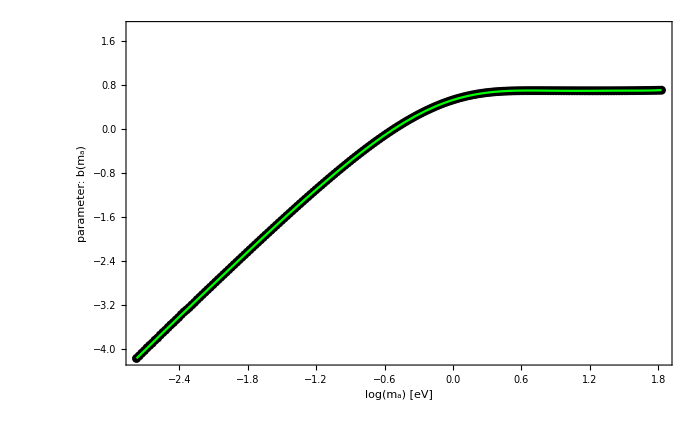

```mathematica
(********************************************* deal with parameter b ****************************************************)
(*Combine maValuesList and AparameterList into a list of points*)
dataParameterb = Transpose[{Log[maValuesList],bparameterList}]; 
(*Use FindFormula to find a suitable model for the data*)
polyModb=LinearModelFit[dataParameterb,Table[x^i,{i,1,11}],x]
polyModb["BestFit"]

(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[dataParameterb];
xmax = Max[Log[maValuesList]];
ymax = Max[dataParameterb];
input=Log[maValuesList];
(******** plotting ********)
Show[ListPlot[dataParameterb,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: b(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700],
Plot[polyModb[x],{x,Min@input,Max@input},PlotStyle->Green]
]
```

FittedModel[0.575443-0.174626 x+0.157016 x^2-0.288267 x^3+0.117304 x^4+«8»+0.00281883 x^10+0.0006214 x^11-0.000048307 x^12]

0.575443-0.174626 x+0.157016 x^2-0.288267 x^3+0.117304 x^4+0.0114396 x^5+0.0433722 x^6-0.00741922 x^7-0.0170838 x^8-0.00324639 x^9+0.00281883 x^10+0.0006214 x^11-0.000048307 x^12

34.2069

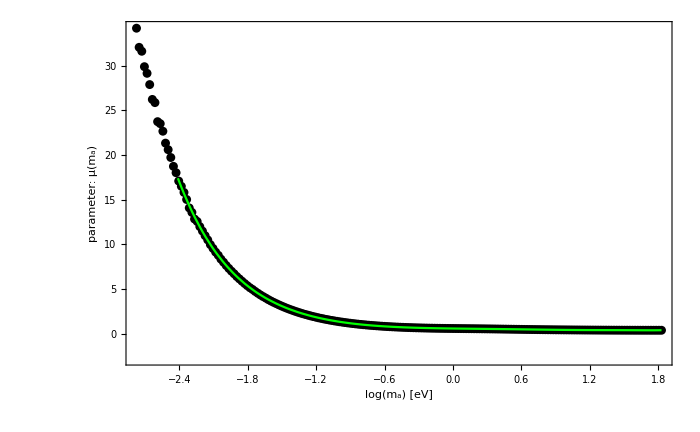

```mathematica
(********************************************* deal with parameter μ ****************************************************)
(*Combine maValuesList and AparameterList into a list of points*)
dataParameterμ = Transpose[{Log[maValuesList],μparameterList}]; 
(*Use FindFormula to find a suitable model for the data*)
polyModμ=LinearModelFit[dataParameterμ,Table[x^i,{i,1,12}],x]
polyModμ["BestFit"]

(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[dataParameterμ];
xmax = Max[Log[maValuesList]];
ymax = Max[dataParameterμ]
input=Log[maValuesList];
(******** plotting ********)
Show[ListPlot[dataParameterμ,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: μ(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700],
Plot[polyModμ[x],{x,Min@input,Max@input},PlotStyle->Green]
]
```

## Second interpolation

{{Null},{Null}}

A = Int of q^3 f(q) (MAXIM): 5.43456

B = Int of x^2(Exp[A√(1 + SuperscriptBox[x, 2])-b]+μ)^-1: 5.46573

|A-B| / A = 0.573448 %

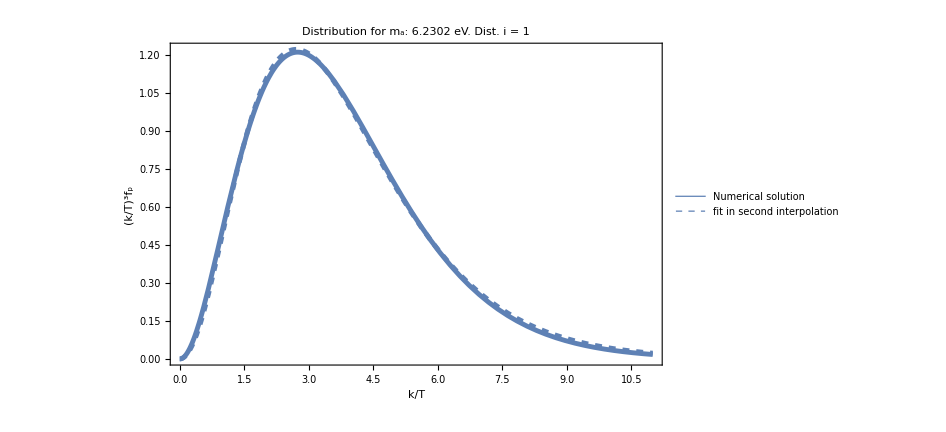

```mathematica
(********** Select distribution that we already have **********)
NumberOfDist = 1;
SelectedDist = AxDistFunctionList[[NumberOfDist]];
SelectedMass = maValuesList[[NumberOfDist]];
(********** Numerical Solution in second interpolation **********)
Avalue = polyModA[Log[SelectedMass]];
{{bvalue = polyModb[Log[SelectedMass]];}, {μvalue = polyModμ[Log[SelectedMass]];}}

(********** Compute the integral of the selected distributions **********)
upperLimit=13;
Print["A = Int of q^3 f(q) (MAXIM): ",integralF=NIntegrate[SelectedDist[x],{x,0,upperLimit}]]
Print["B = Int of x^2(Exp[A√(1 + SuperscriptBox[x, 2])-b]+μ)^-1: ",integralFit = NIntegrate[fApprox[x,Avalue,bvalue,μvalue],{x,0,upperLimit}]]
Print["|A-B| / A = ", Abs[integralF -integralFit]/ integralF *100, " %"]
(********** Plot distribution and fit **********)
Plot[{SelectedDist[x], fApprox[x,Avalue,bvalue,μvalue]},{x,0,11},Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},{Dashed,Thickness[0.005],ColorData[97,1]},{Thickness[0.005],Orange,ColorData[97,2]}},

PlotLegends->{"Numerical solution","fit in second interpolation"},
PlotLabel->"Distribution for m_a: "  <> ToString[SelectedMass] <> " eV. Dist. i = " <> ToString [NumberOfDist],
ImageSize-> 700]
```

## Comparison to Bose-Einstein and Boltzmann distribution

Part::partd: Part specification faValuesList⟦1⟧ is longer than depth of object.

f_a: faValuesList⟦1⟧ GeV

{{Null},{Null}}

5.43456

NIntegrate::inumr: The integrand C ⅇ^-x x^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,13}}.

{C→0.906712}

NIntegrate::inumr: The integrand (C x^3)/(-1+ⅇ^x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,13}}.

{C→0.837679}

{C→0.906712}

{C→0.837679}

5.43456

5.43456

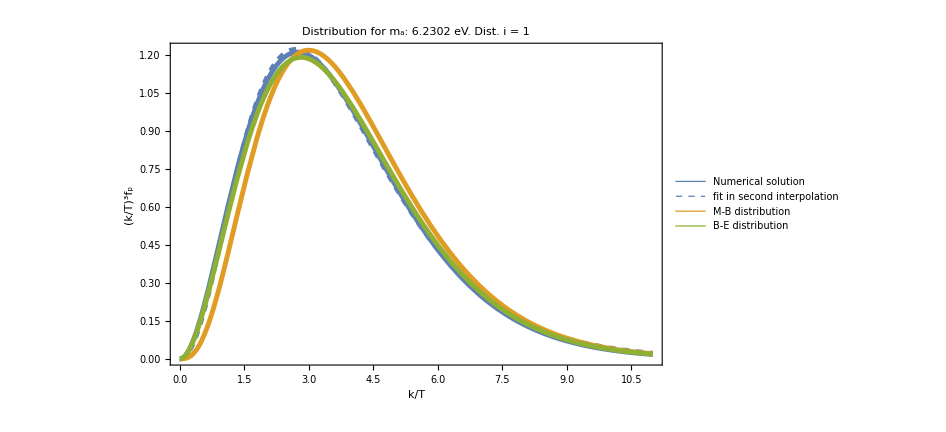

```mathematica
(********** Select distribution that we already have **********)
NumberOfDist=1;
SelectedDist=AxDistFunctionList[[NumberOfDist]];
SelectedMass=maValuesList[[NumberOfDist]];
SelectedFa = faValuesList[[NumberOfDist]];
Print["f_a: ", SelectedFa, " GeV"]
(********** Numerical Solution in second interpolation **********)
Avalue = polyModA[Log[SelectedMass]];
{{bvalue = polyModb[Log[SelectedMass]];}, {μvalue = polyModμ[Log[SelectedMass]];}}

(********** Define the distribution functions **********)
fBoltzmann[C_,x_]:=x^3 C Exp[- x]
fEinstein[C_,x_]:=x^3 C(Exp[x]-1)^(-1)

(********** Compute the integral of the selected distribution **********)
upperLimit=13;
integralF=NIntegrate[SelectedDist[x],{x,0,upperLimit}]

(********** Define the numerical integrals for the other functions **********)
integralFBoltzmann[C_]:=NIntegrate[fBoltzmann[C,x],{x,0,upperLimit}]
integralFEinstein[C_]:=NIntegrate[fEinstein[C,x],{x,0,upperLimit}]

(********** Solve for C using FindRoot **********)
solBoltzmann=FindRoot[integralF==integralFBoltzmann[C],{C,1}]
solEinstein=FindRoot[integralF==integralFEinstein[C],{C,1}]

(********** Display the solutions **********)
solBoltzmann
solEinstein

(********** Verify the solutions **********)
NIntegrate[fBoltzmann[C/. solBoltzmann,x],{x,0,upperLimit}]
NIntegrate[fEinstein[C/. solEinstein,x],{x,0,upperLimit}]

(********** Plot: Compare fit to Bose-Eintesin and Maxwell-Boltzmann distribution **********)
Plot[{SelectedDist[x], fApprox[x,Avalue,bvalue,μvalue], 
fBoltzmann[C/. solBoltzmann, x], 
fEinstein[C/. solEinstein, x]},{x,0,11},
Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},{Dashed,Thickness[0.005],ColorData[97,1]},
{Thickness[0.005],Orange,ColorData[97,2]},{Thickness[0.005],Green,ColorData[97,3]}},

PlotLegends->{"Numerical solution","fit in second interpolation", "M-B distribution", "B-E distribution"},
PlotLabel->"Distribution for m_a: "  <> ToString[SelectedMass] <> " eV. Dist. i = " <> ToString [NumberOfDist],
ImageSize-> 700]
```